# Runtime Testing

```mathematica
<<StoChemSim`
```

## Direct SSA

All system constructions have number of reactions = number of species.

```mathematica
(*System 1: Every species appears in precisely 1 reaction. Every reaction has only 1 reactant and 1 product.*)
ConstructSys1[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[x[i],y[i],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 2: Every species appears in O(sqrt(n)) reactions. Every reaction has O(sqrt(n)) reactants and O(sqrt(n)) products.*)
ConstructSys2[n_]:=Module[
{k,rxns,xConcs,yConcs,concs},
k=Round[Sqrt[n]];
rxns= Flatten[Table[revrxn[Plus@@Table[x[i,l]+x[j,l],{l,k}],Plus@@Table[y[i,l]+y[j,l],{l,k}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,k},{j,k}]];
xConcs=Flatten[Table[conc[x[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
yConcs=Flatten[Table[conc[y[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 3: Every species appears in all reactions. Every reaction has O(n) reactants and O(n) products.*)
ConstructSys3[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[Plus@@Table[x[j],{j,n}],Plus@@Table[y[j],{j,n}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
TestSysSSA[construction_,kRange_,iters_,statesOnlyFlag_]:=Module[{},
Table[Module[
{n,rxns,concs,rxnsys,nRxns,nSpecies,results,totalTime,runtimeInfo,timePerIter,algoTimePerIter,out},
n=k^2;
{rxns,concs} = construction[n];
rxnsys=Flatten[{rxns,concs}];
nRxns=Length[ExpandRevrxns[rxns]];
nSpecies=Length[SpeciesInRxnsys[rxnsys]];
results=Timing[SimulateDirectSSA[rxnsys,useIter->True,iterEnd->iters,statesOnly->statesOnlyFlag,finalOnly->True,outputTS->False]];
totalTime=results[[1]];
runtimeInfo=GetRuntimeInfo[];
timePerIter=runtimeInfo["backend algorithm"]/iters;
out={construction,statesOnlyFlag,nRxns,nSpecies,iters,totalTime,timePerIter,runtimeInfo};
Print[out];
out],
{k,kRange}]]
```

## Constructions 1, 2, and 3 up to 200 reactions

```mathematica
constructions={ConstructSys1,ConstructSys2,ConstructSys3};
kRange={1,3,5,10};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.109375,1.08499×10^-6,<|frontend conversion→0.,interface conversion→6.×10^-6,backend preprocessing→0.0000452,backend algorithm→0.108499|>}

{ConstructSys1,False,18,18,100000,0.21875,2.21834×10^-6,<|frontend conversion→0.,interface conversion→0.0000299,backend preprocessing→0.0000527,backend algorithm→0.221834|>}

{ConstructSys1,False,50,50,100000,0.46875,4.51112×10^-6,<|frontend conversion→0.015625,interface conversion→0.000073,backend preprocessing→0.0006146,backend algorithm→0.451112|>}

{ConstructSys1,False,200,200,100000,1.48438,0.0000144689,<|frontend conversion→0.03125,interface conversion→0.0001522,backend preprocessing→0.0002479,backend algorithm→1.44689|>}

{ConstructSys1,True,2,2,100000,0.09375,9.67306×10^-7,<|frontend conversion→0.,interface conversion→6.6×10^-6,backend preprocessing→0.0000332,backend algorithm→0.0967306|>}

{ConstructSys1,True,18,18,100000,0.21875,2.18151×10^-6,<|frontend conversion→0.,interface conversion→0.0000285,backend preprocessing→0.000037,backend algorithm→0.218151|>}

{ConstructSys1,True,50,50,100000,0.46875,4.57069×10^-6,<|frontend conversion→0.015625,interface conversion→0.000067,backend preprocessing→0.0001357,backend algorithm→0.457069|>}

{ConstructSys1,True,200,200,100000,1.48438,0.0000145477,<|frontend conversion→0.03125,interface conversion→0.0002374,backend preprocessing→0.0019278,backend algorithm→1.45477|>}

{ConstructSys2,False,2,2,100000,0.109375,1.12116×10^-6,<|frontend conversion→0.,interface conversion→5.2×10^-6,backend preprocessing→0.0000286,backend algorithm→0.112116|>}

{ConstructSys2,False,18,18,100000,0.59375,5.98864×10^-6,<|frontend conversion→0.,interface conversion→0.0000776,backend preprocessing→0.000091,backend algorithm→0.598864|>}

{ConstructSys2,False,50,50,100000,1.28125,0.0000127497,<|frontend conversion→0.015625,interface conversion→0.0002178,backend preprocessing→0.0004623,backend algorithm→1.27497|>}

{ConstructSys2,False,200,200,100000,4.15625,0.0000408631,<|frontend conversion→0.0625,interface conversion→0.0012935,backend preprocessing→0.0020867,backend algorithm→4.08631|>}

{ConstructSys2,True,2,2,100000,0.109375,1.03635×10^-6,<|frontend conversion→0.,interface conversion→8.1×10^-6,backend preprocessing→0.0000314,backend algorithm→0.103635|>}

{ConstructSys2,True,18,18,100000,0.671875,6.71435×10^-6,<|frontend conversion→0.,interface conversion→0.0000364,backend preprocessing→0.0001086,backend algorithm→0.671435|>}

{ConstructSys2,True,50,50,100000,1.5625,0.0000159285,<|frontend conversion→0.015625,interface conversion→0.0002,backend preprocessing→0.0003136,backend algorithm→1.59285|>}

{ConstructSys2,True,200,200,100000,4.90625,0.0000486232,<|frontend conversion→0.09375,interface conversion→0.000827,backend preprocessing→0.0014107,backend algorithm→4.86232|>}

{ConstructSys3,False,2,2,100000,0.109375,1.28144×10^-6,<|frontend conversion→0.,interface conversion→0.0000381,backend preprocessing→0.0000829,backend algorithm→0.128144|>}

{ConstructSys3,False,18,18,100000,1.07813,0.0000110059,<|frontend conversion→0.,interface conversion→0.0000941,backend preprocessing→0.0001926,backend algorithm→1.10059|>}

{ConstructSys3,False,50,50,100000,2.46875,0.0000243572,<|frontend conversion→0.03125,interface conversion→0.0002938,backend preprocessing→0.0006194,backend algorithm→2.43572|>}

{ConstructSys3,False,200,200,100000,19.5625,0.000203046,<|frontend conversion→0.203125,interface conversion→0.0031049,backend preprocessing→0.0087019,backend algorithm→20.3046|>}

{ConstructSys3,True,2,2,100000,0.15625,1.55714×10^-6,<|frontend conversion→0.015625,interface conversion→9.2×10^-6,backend preprocessing→0.0000344,backend algorithm→0.155714|>}

{ConstructSys3,True,18,18,100000,1.04688,0.0000104725,<|frontend conversion→0.015625,interface conversion→0.0001104,backend preprocessing→0.0000948,backend algorithm→1.04725|>}

{ConstructSys3,True,50,50,100000,3.34375,0.0000417835,<|frontend conversion→0.015625,interface conversion→0.0002734,backend preprocessing→0.0005309,backend algorithm→4.17835|>}

{ConstructSys3,True,200,200,100000,19.75,0.000207672,<|frontend conversion→0.21875,interface conversion→0.0018021,backend preprocessing→0.0116396,backend algorithm→20.7672|>}

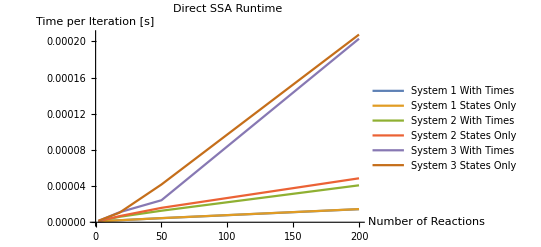

```mathematica
coorsSSA=Flatten[Table[
Table[{resultsSSA[[i]][[j]][[l]][[3]],resultsSSA[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1","System 2","System 3"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA.mx"},OperatingSystem->$OperatingSystem], resultsSSA];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA.mx"},OperatingSystem->$OperatingSystem], coorsSSA];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.109375,1.08499×10^-6,<|frontend conversion→0.,interface conversion→6.×10^-6,backend preprocessing→0.0000452,backend algorithm→0.108499|>},{ConstructSys1,False,18,18,100000,0.21875,2.21834×10^-6,<|frontend conversion→0.,interface conversion→0.0000299,backend preprocessing→0.0000527,backend algorithm→0.221834|>},{ConstructSys1,False,50,50,100000,0.46875,4.51112×10^-6,<|frontend conversion→0.015625,interface conversion→0.000073,backend preprocessing→0.0006146,backend algorithm→0.451112|>},{ConstructSys1,False,200,200,100000,1.48438,0.0000144689,<|frontend conversion→0.03125,interface conversion→0.0001522,backend preprocessing→0.0002479,backend algorithm→1.44689|>}},{{ConstructSys1,True,2,2,100000,0.09375,9.67306×10^-7,<|frontend conversion→0.,interface conversion→6.6×10^-6,backend preprocessing→0.0000332,backend algorithm→0.0967306|>},{ConstructSys1,True,18,18,100000,0.21875,2.18151×10^-6,<|frontend conversion→0.,interface conversion→0.0000285,backend preprocessing→0.000037,backend algorithm→0.218151|>},{ConstructSys1,True,50,50,100000,0.46875,4.57069×10^-6,<|frontend conversion→0.015625,interface conversion→0.000067,backend preprocessing→0.0001357,backend algorithm→0.457069|>},{ConstructSys1,True,200,200,100000,1.48438,0.0000145477,<|frontend conversion→0.03125,interface conversion→0.0002374,backend preprocessing→0.0019278,backend algorithm→1.45477|>}}},{{{ConstructSys2,False,2,2,100000,0.109375,1.12116×10^-6,<|frontend conversion→0.,interface conversion→5.2×10^-6,backend preprocessing→0.0000286,backend algorithm→0.112116|>},{ConstructSys2,False,18,18,100000,0.59375,5.98864×10^-6,<|frontend conversion→0.,interface conversion→0.0000776,backend preprocessing→0.000091,backend algorithm→0.598864|>},{ConstructSys2,False,50,50,100000,1.28125,0.0000127497,<|frontend conversion→0.015625,interface conversion→0.0002178,backend preprocessing→0.0004623,backend algorithm→1.27497|>},{ConstructSys2,False,200,200,100000,4.15625,0.0000408631,<|frontend conversion→0.0625,interface conversion→0.0012935,backend preprocessing→0.0020867,backend algorithm→4.08631|>}},{{ConstructSys2,True,2,2,100000,0.109375,1.03635×10^-6,<|frontend conversion→0.,interface conversion→8.1×10^-6,backend preprocessing→0.0000314,backend algorithm→0.103635|>},{ConstructSys2,True,18,18,100000,0.671875,6.71435×10^-6,<|frontend conversion→0.,interface conversion→0.0000364,backend preprocessing→0.0001086,backend algorithm→0.671435|>},{ConstructSys2,True,50,50,100000,1.5625,0.0000159285,<|frontend conversion→0.015625,interface conversion→0.0002,backend preprocessing→0.0003136,backend algorithm→1.59285|>},{ConstructSys2,True,200,200,100000,4.90625,0.0000486232,<|frontend conversion→0.09375,interface conversion→0.000827,backend preprocessing→0.0014107,backend algorithm→4.86232|>}}},{{{ConstructSys3,False,2,2,100000,0.109375,1.28144×10^-6,<|frontend conversion→0.,interface conversion→0.0000381,backend preprocessing→0.0000829,backend algorithm→0.128144|>},{ConstructSys3,False,18,18,100000,1.07813,0.0000110059,<|frontend conversion→0.,interface conversion→0.0000941,backend preprocessing→0.0001926,backend algorithm→1.10059|>},{ConstructSys3,False,50,50,100000,2.46875,0.0000243572,<|frontend conversion→0.03125,interface conversion→0.0002938,backend preprocessing→0.0006194,backend algorithm→2.43572|>},{ConstructSys3,False,200,200,100000,19.5625,0.000203046,<|frontend conversion→0.203125,interface conversion→0.0031049,backend preprocessing→0.0087019,backend algorithm→20.3046|>}},{{ConstructSys3,True,2,2,100000,0.15625,1.55714×10^-6,<|frontend conversion→0.015625,interface conversion→9.2×10^-6,backend preprocessing→0.0000344,backend algorithm→0.155714|>},{ConstructSys3,True,18,18,100000,1.04688,0.0000104725,<|frontend conversion→0.015625,interface conversion→0.0001104,backend preprocessing→0.0000948,backend algorithm→1.04725|>},{ConstructSys3,True,50,50,100000,3.34375,0.0000417835,<|frontend conversion→0.015625,interface conversion→0.0002734,backend preprocessing→0.0005309,backend algorithm→4.17835|>},{ConstructSys3,True,200,200,100000,19.75,0.000207672,<|frontend conversion→0.21875,interface conversion→0.0018021,backend preprocessing→0.0116396,backend algorithm→20.7672|>}}}}

{{{2,1.08499×10^-6},{18,2.21834×10^-6},{50,4.51112×10^-6},{200,0.0000144689}},{{2,9.67306×10^-7},{18,2.18151×10^-6},{50,4.57069×10^-6},{200,0.0000145477}},{{2,1.12116×10^-6},{18,5.98864×10^-6},{50,0.0000127497},{200,0.0000408631}},{{2,1.03635×10^-6},{18,6.71435×10^-6},{50,0.0000159285},{200,0.0000486232}},{{2,1.28144×10^-6},{18,0.0000110059},{50,0.0000243572},{200,0.000203046}},{{2,1.55714×10^-6},{18,0.0000104725},{50,0.0000417835},{200,0.000207672}}}

## Constructions 1 and 2 up to 1,250 reactions

```mathematica
constructions={ConstructSys1,ConstructSys2};
kRange={1,3,5,10,25};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA2=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.09375,9.9569×10^-7,<|frontend conversion→0.,interface conversion→0.0000169,backend preprocessing→0.0000259,backend algorithm→0.099569|>}

{ConstructSys1,False,18,18,100000,0.21875,2.19915×10^-6,<|frontend conversion→0.,interface conversion→0.0000191,backend preprocessing→0.0000476,backend algorithm→0.219915|>}

{ConstructSys1,False,50,50,100000,0.5,4.96592×10^-6,<|frontend conversion→0.015625,interface conversion→0.0000671,backend preprocessing→0.000106,backend algorithm→0.496592|>}

{ConstructSys1,False,200,200,100000,1.57813,0.0000154881,<|frontend conversion→0.03125,interface conversion→0.0002971,backend preprocessing→0.0006804,backend algorithm→1.54881|>}

{ConstructSys1,False,1250,1250,100000,10.5156,0.000110534,<|frontend conversion→0.34375,interface conversion→0.004088,backend preprocessing→0.0015733,backend algorithm→11.0534|>}

{ConstructSys1,True,2,2,100000,0.09375,1.05558×10^-6,<|frontend conversion→0.,interface conversion→7.1×10^-6,backend preprocessing→0.0000298,backend algorithm→0.105558|>}

{ConstructSys1,True,18,18,100000,0.234375,2.38533×10^-6,<|frontend conversion→0.,interface conversion→0.0000196,backend preprocessing→0.0000975,backend algorithm→0.238533|>}

{ConstructSys1,True,50,50,100000,0.515625,5.13692×10^-6,<|frontend conversion→0.,interface conversion→0.0000802,backend preprocessing→0.0001475,backend algorithm→0.513692|>}

{ConstructSys1,True,200,200,100000,1.92188,0.0000209468,<|frontend conversion→0.015625,interface conversion→0.0002872,backend preprocessing→0.0003949,backend algorithm→2.09468|>}

{ConstructSys1,True,1250,1250,100000,10.7344,0.000111109,<|frontend conversion→0.359375,interface conversion→0.0045701,backend preprocessing→0.0023656,backend algorithm→11.1109|>}

{ConstructSys2,False,2,2,100000,0.15625,1.83332×10^-6,<|frontend conversion→0.,interface conversion→0.0000187,backend preprocessing→0.0000395,backend algorithm→0.183332|>}

{ConstructSys2,False,18,18,100000,0.71875,7.32821×10^-6,<|frontend conversion→0.,interface conversion→0.0000522,backend preprocessing→0.0000817,backend algorithm→0.732821|>}

{ConstructSys2,False,50,50,100000,1.73438,0.0000190859,<|frontend conversion→0.015625,interface conversion→0.0001778,backend preprocessing→0.0003118,backend algorithm→1.90859|>}

{ConstructSys2,False,200,200,100000,5.10938,0.0000515741,<|frontend conversion→0.078125,interface conversion→0.0007583,backend preprocessing→0.0010307,backend algorithm→5.15741|>}

{ConstructSys2,False,1250,1250,100000,33.875,0.000337835,<|frontend conversion→1.03125,interface conversion→0.0095142,backend preprocessing→0.0149438,backend algorithm→33.7835|>}

{ConstructSys2,True,2,2,100000,0.171875,1.19679×10^-6,<|frontend conversion→0.046875,interface conversion→0.0000102,backend preprocessing→0.0000361,backend algorithm→0.119679|>}

{ConstructSys2,True,18,18,100000,1.40625,0.000014684,<|frontend conversion→0.,interface conversion→0.0001552,backend preprocessing→0.0000577,backend algorithm→1.4684|>}

{ConstructSys2,True,50,50,100000,1.65625,0.0000171988,<|frontend conversion→0.,interface conversion→0.0001811,backend preprocessing→0.0003986,backend algorithm→1.71988|>}

{ConstructSys2,True,200,200,100000,5.32813,0.0000535051,<|frontend conversion→0.078125,interface conversion→0.0006058,backend preprocessing→0.0008673,backend algorithm→5.35051|>}

{ConstructSys2,True,1250,1250,100000,34.2813,0.000335318,<|frontend conversion→1.39063,interface conversion→0.0095274,backend preprocessing→0.026048,backend algorithm→33.5318|>}

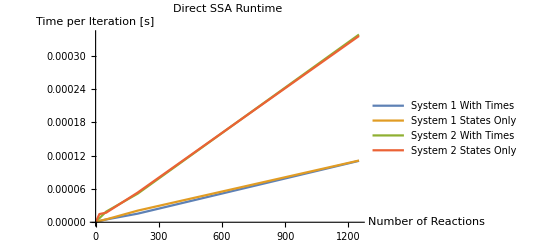

```mathematica
coorsSSA2=Flatten[Table[
Table[{resultsSSA2[[i]][[j]][[l]][[3]],resultsSSA2[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA2[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1","System 2"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA2,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA2.mx"},OperatingSystem->$OperatingSystem], resultsSSA2];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA2.mx"},OperatingSystem->$OperatingSystem], coorsSSA2];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA2=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA2.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA2=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA2.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.09375,9.9569×10^-7,<|frontend conversion→0.,interface conversion→0.0000169,backend preprocessing→0.0000259,backend algorithm→0.099569|>},{ConstructSys1,False,18,18,100000,0.21875,2.19915×10^-6,<|frontend conversion→0.,interface conversion→0.0000191,backend preprocessing→0.0000476,backend algorithm→0.219915|>},{ConstructSys1,False,50,50,100000,0.5,4.96592×10^-6,<|frontend conversion→0.015625,interface conversion→0.0000671,backend preprocessing→0.000106,backend algorithm→0.496592|>},{ConstructSys1,False,200,200,100000,1.57813,0.0000154881,<|frontend conversion→0.03125,interface conversion→0.0002971,backend preprocessing→0.0006804,backend algorithm→1.54881|>},{ConstructSys1,False,1250,1250,100000,10.5156,0.000110534,<|frontend conversion→0.34375,interface conversion→0.004088,backend preprocessing→0.0015733,backend algorithm→11.0534|>}},{{ConstructSys1,True,2,2,100000,0.09375,1.05558×10^-6,<|frontend conversion→0.,interface conversion→7.1×10^-6,backend preprocessing→0.0000298,backend algorithm→0.105558|>},{ConstructSys1,True,18,18,100000,0.234375,2.38533×10^-6,<|frontend conversion→0.,interface conversion→0.0000196,backend preprocessing→0.0000975,backend algorithm→0.238533|>},{ConstructSys1,True,50,50,100000,0.515625,5.13692×10^-6,<|frontend conversion→0.,interface conversion→0.0000802,backend preprocessing→0.0001475,backend algorithm→0.513692|>},{ConstructSys1,True,200,200,100000,1.92188,0.0000209468,<|frontend conversion→0.015625,interface conversion→0.0002872,backend preprocessing→0.0003949,backend algorithm→2.09468|>},{ConstructSys1,True,1250,1250,100000,10.7344,0.000111109,<|frontend conversion→0.359375,interface conversion→0.0045701,backend preprocessing→0.0023656,backend algorithm→11.1109|>}}},{{{ConstructSys2,False,2,2,100000,0.15625,1.83332×10^-6,<|frontend conversion→0.,interface conversion→0.0000187,backend preprocessing→0.0000395,backend algorithm→0.183332|>},{ConstructSys2,False,18,18,100000,0.71875,7.32821×10^-6,<|frontend conversion→0.,interface conversion→0.0000522,backend preprocessing→0.0000817,backend algorithm→0.732821|>},{ConstructSys2,False,50,50,100000,1.73438,0.0000190859,<|frontend conversion→0.015625,interface conversion→0.0001778,backend preprocessing→0.0003118,backend algorithm→1.90859|>},{ConstructSys2,False,200,200,100000,5.10938,0.0000515741,<|frontend conversion→0.078125,interface conversion→0.0007583,backend preprocessing→0.0010307,backend algorithm→5.15741|>},{ConstructSys2,False,1250,1250,100000,33.875,0.000337835,<|frontend conversion→1.03125,interface conversion→0.0095142,backend preprocessing→0.0149438,backend algorithm→33.7835|>}},{{ConstructSys2,True,2,2,100000,0.171875,1.19679×10^-6,<|frontend conversion→0.046875,interface conversion→0.0000102,backend preprocessing→0.0000361,backend algorithm→0.119679|>},{ConstructSys2,True,18,18,100000,1.40625,0.000014684,<|frontend conversion→0.,interface conversion→0.0001552,backend preprocessing→0.0000577,backend algorithm→1.4684|>},{ConstructSys2,True,50,50,100000,1.65625,0.0000171988,<|frontend conversion→0.,interface conversion→0.0001811,backend preprocessing→0.0003986,backend algorithm→1.71988|>},{ConstructSys2,True,200,200,100000,5.32813,0.0000535051,<|frontend conversion→0.078125,interface conversion→0.0006058,backend preprocessing→0.0008673,backend algorithm→5.35051|>},{ConstructSys2,True,1250,1250,100000,34.2813,0.000335318,<|frontend conversion→1.39063,interface conversion→0.0095274,backend preprocessing→0.026048,backend algorithm→33.5318|>}}}}

{{{2,9.9569×10^-7},{18,2.19915×10^-6},{50,4.96592×10^-6},{200,0.0000154881},{1250,0.000110534}},{{2,1.05558×10^-6},{18,2.38533×10^-6},{50,5.13692×10^-6},{200,0.0000209468},{1250,0.000111109}},{{2,1.83332×10^-6},{18,7.32821×10^-6},{50,0.0000190859},{200,0.0000515741},{1250,0.000337835}},{{2,1.19679×10^-6},{18,0.000014684},{50,0.0000171988},{200,0.0000535051},{1250,0.000335318}}}

## Construction 1 up to 20,000 reactions

```mathematica
constructions={ConstructSys1};
kRange={1,3,5,10,25,50,100};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA3=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.21875,1.78942×10^-6,<|frontend conversion→0.046875,interface conversion→9.6×10^-6,backend preprocessing→0.0000302,backend algorithm→0.178942|>}

{ConstructSys1,False,18,18,100000,0.390625,4.1304×10^-6,<|frontend conversion→0.,interface conversion→0.0000283,backend preprocessing→0.0000502,backend algorithm→0.41304|>}

{ConstructSys1,False,50,50,100000,0.515625,5.11652×10^-6,<|frontend conversion→0.,interface conversion→0.000113,backend preprocessing→0.0001263,backend algorithm→0.511652|>}

{ConstructSys1,False,200,200,100000,1.59375,0.0000158141,<|frontend conversion→0.015625,interface conversion→0.0002775,backend preprocessing→0.0003927,backend algorithm→1.58141|>}

{ConstructSys1,False,1250,1250,100000,10.875,0.000108521,<|frontend conversion→0.359375,interface conversion→0.0043964,backend preprocessing→0.0020309,backend algorithm→10.8521|>}

{ConstructSys1,False,5000,5000,100000,53.5313,0.000494869,<|frontend conversion→4.6875,interface conversion→0.0382926,backend preprocessing→0.0142754,backend algorithm→49.4869|>}

{ConstructSys1,False,20000,20000,100000,290.438,0.00221398,<|frontend conversion→73.8594,interface conversion→0.889473,backend preprocessing→1.22239,backend algorithm→221.398|>}

{ConstructSys1,True,2,2,100000,0.140625,1.40078×10^-6,<|frontend conversion→0.,interface conversion→0.0000144,backend preprocessing→0.0001385,backend algorithm→0.140078|>}

{ConstructSys1,True,18,18,100000,0.28125,2.86479×10^-6,<|frontend conversion→0.,interface conversion→0.0000343,backend preprocessing→0.0001659,backend algorithm→0.286479|>}

{ConstructSys1,True,50,50,100000,0.53125,5.24743×10^-6,<|frontend conversion→0.,interface conversion→0.0000825,backend preprocessing→0.0004423,backend algorithm→0.524743|>}

{ConstructSys1,True,200,200,100000,1.78125,0.0000177354,<|frontend conversion→0.03125,interface conversion→0.0004313,backend preprocessing→0.0011409,backend algorithm→1.77354|>}

{ConstructSys1,True,1250,1250,100000,9.90625,0.0000953045,<|frontend conversion→0.390625,interface conversion→0.0031997,backend preprocessing→0.002043,backend algorithm→9.53045|>}

{ConstructSys1,True,5000,5000,100000,59.0469,0.000596238,<|frontend conversion→4.5,interface conversion→0.0392085,backend preprocessing→0.0148463,backend algorithm→59.6238|>}

{ConstructSys1,True,20000,20000,100000,305.141,0.00216182,<|frontend conversion→90.7969,interface conversion→1.04159,backend preprocessing→0.924782,backend algorithm→216.182|>}

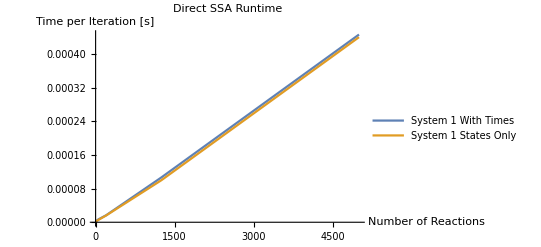

```mathematica
coorsSSA3=Flatten[Table[
Table[{resultsSSA3[[i]][[j]][[l]][[3]],resultsSSA3[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA3[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA3,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA3.mx"},OperatingSystem->$OperatingSystem], resultsSSA3];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA3.mx"},OperatingSystem->$OperatingSystem], coorsSSA3];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA3=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA3.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA3=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA3.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.109375,1.06228×10^-6,<|frontend conversion→0.,interface conversion→6.6×10^-6,backend preprocessing→0.0000257,backend algorithm→0.106228|>},{ConstructSys1,False,18,18,100000,0.34375,3.49077×10^-6,<|frontend conversion→0.,interface conversion→0.0000221,backend preprocessing→0.0000431,backend algorithm→0.349077|>},{ConstructSys1,False,50,50,100000,0.65625,6.61675×10^-6,<|frontend conversion→0.,interface conversion→0.0000716,backend preprocessing→0.0001628,backend algorithm→0.661675|>},{ConstructSys1,False,200,200,100000,1.6875,0.0000166129,<|frontend conversion→0.03125,interface conversion→0.0003253,backend preprocessing→0.0004531,backend algorithm→1.66129|>},{ConstructSys1,False,1250,1250,100000,10.375,0.000106795,<|frontend conversion→0.34375,interface conversion→0.0020833,backend preprocessing→0.0015865,backend algorithm→10.6795|>},{ConstructSys1,False,5000,5000,100000,49.3906,0.000446758,<|frontend conversion→4.90625,interface conversion→0.032083,backend preprocessing→0.0165411,backend algorithm→44.6758|>}},{{ConstructSys1,True,2,2,100000,0.109375,1.18653×10^-6,<|frontend conversion→0.015625,interface conversion→9.×10^-6,backend preprocessing→0.0000372,backend algorithm→0.118653|>},{ConstructSys1,True,18,18,100000,0.28125,2.93299×10^-6,<|frontend conversion→0.,interface conversion→0.000022,backend preprocessing→0.0000636,backend algorithm→0.293299|>},{ConstructSys1,True,50,50,100000,0.546875,5.39579×10^-6,<|frontend conversion→0.,interface conversion→0.0000773,backend preprocessing→0.0004909,backend algorithm→0.539579|>},{ConstructSys1,True,200,200,100000,1.60938,0.0000161482,<|frontend conversion→0.03125,interface conversion→0.0003014,backend preprocessing→0.0005063,backend algorithm→1.61482|>},{ConstructSys1,True,1250,1250,100000,10.2969,0.000100154,<|frontend conversion→0.34375,interface conversion→0.0024798,backend preprocessing→0.0019081,backend algorithm→10.0154|>},{ConstructSys1,True,5000,5000,100000,48.5469,0.000440559,<|frontend conversion→4.5,interface conversion→0.0366917,backend preprocessing→0.0200542,backend algorithm→44.0559|>}}}}

{{{2,1.06228×10^-6},{18,3.49077×10^-6},{50,6.61675×10^-6},{200,0.0000166129},{1250,0.000106795},{5000,0.000446758}},{{2,1.18653×10^-6},{18,2.93299×10^-6},{50,5.39579×10^-6},{200,0.0000161482},{1250,0.000100154},{5000,0.000440559}}}

## Bounded Tau Leaping

```mathematica
<<StoChemSim`
```

```mathematica
ConstructSysMax[n_]:={
rxnl[{x1},{y,z1},1],
rxnl[{x2},{y,z2},1],
rxnl[{z1,z2},{k},1/n],
rxnl[{k,y},{},1/n],
conc[{x1,x2},n/2]
};
```

```mathematica
TestSysBTL[construction_,simulation_,nRange_]:=Module[{},
Table[Module[
{rxnsys,results,totalTime,runtimeInfo,algoTime},
rxnsys= construction[n];
results=Timing[simulation[rxnsys,finalOnly->True,outputTS->False]];
totalTime=results[[1]];
runtimeInfo=GetRuntimeInfo[];
out={simulation,n,totalTime,runtimeInfo};
Print[out];
out],
{n,nRange}]]
```

## Direct SSA vs. BTL up to 32,768 molecules

```mathematica
simulations={SimulateDirectSSA,SimulateBoundedTauLeaping};
nRange=Table[2^i,{i,1,15}];
resultsBTL=Table[TestSysBTL[ConstructSysMax,simulations[[i]],nRange],{i,Length[simulations]}];
```

{SimulateDirectSSA,2,0.,<|frontend conversion→0.,interface conversion→0.0000133,backend preprocessing→0.000243,backend algorithm→0.0004158|>}

{SimulateDirectSSA,4,0.,<|frontend conversion→0.,interface conversion→0.0000151,backend preprocessing→0.000108,backend algorithm→0.0000146|>}

{SimulateDirectSSA,8,0.,<|frontend conversion→0.,interface conversion→8.9×10^-6,backend preprocessing→0.0000183,backend algorithm→0.000022|>}

{SimulateDirectSSA,16,0.,<|frontend conversion→0.,interface conversion→8.2×10^-6,backend preprocessing→0.0000152,backend algorithm→0.0000457|>}

{SimulateDirectSSA,32,0.015625,<|frontend conversion→0.,interface conversion→8.1×10^-6,backend preprocessing→0.0000175,backend algorithm→0.0000794|>}

{SimulateDirectSSA,64,0.,<|frontend conversion→0.,interface conversion→8.3×10^-6,backend preprocessing→0.0000154,backend algorithm→0.0001772|>}

{SimulateDirectSSA,128,0.,<|frontend conversion→0.,interface conversion→0.0000148,backend preprocessing→0.0000335,backend algorithm→0.0006223|>}

{SimulateDirectSSA,256,0.,<|frontend conversion→0.,interface conversion→0.0000237,backend preprocessing→0.0000353,backend algorithm→0.0013147|>}

{SimulateDirectSSA,512,0.,<|frontend conversion→0.,interface conversion→0.0000125,backend preprocessing→0.0000278,backend algorithm→0.0025492|>}

{SimulateDirectSSA,1024,0.,<|frontend conversion→0.,interface conversion→0.0000127,backend preprocessing→0.0000296,backend algorithm→0.0032378|>}

{SimulateDirectSSA,2048,0.,<|frontend conversion→0.,interface conversion→9.1×10^-6,backend preprocessing→0.0000557,backend algorithm→0.005855|>}

{SimulateDirectSSA,4096,0.015625,<|frontend conversion→0.,interface conversion→0.0000106,backend preprocessing→0.0000224,backend algorithm→0.0114863|>}

{SimulateDirectSSA,8192,0.03125,<|frontend conversion→0.,interface conversion→0.0000174,backend preprocessing→0.0000349,backend algorithm→0.0288267|>}

{SimulateDirectSSA,16384,0.046875,<|frontend conversion→0.,interface conversion→5.9×10^-6,backend preprocessing→0.000024,backend algorithm→0.0520087|>}

{SimulateDirectSSA,32768,0.09375,<|frontend conversion→0.,interface conversion→0.0000125,backend preprocessing→0.000048,backend algorithm→0.0986989|>}

{SimulateBoundedTauLeaping,2,0.,<|frontend conversion→0.,interface conversion→0.000144,backend preprocessing→0.0000238,backend algorithm→0.0005483|>}

{SimulateBoundedTauLeaping,4,0.,<|frontend conversion→0.,interface conversion→0.0000169,backend preprocessing→5.×10^-6,backend algorithm→0.0001691|>}

{SimulateBoundedTauLeaping,8,0.,<|frontend conversion→0.,interface conversion→0.0000165,backend preprocessing→5.5×10^-6,backend algorithm→0.0003114|>}

{SimulateBoundedTauLeaping,16,0.,<|frontend conversion→0.,interface conversion→0.0000111,backend preprocessing→3.×10^-6,backend algorithm→0.0004659|>}

{SimulateBoundedTauLeaping,32,0.,<|frontend conversion→0.,interface conversion→0.0000199,backend preprocessing→5.3×10^-6,backend algorithm→0.0013937|>}

{SimulateBoundedTauLeaping,64,0.,<|frontend conversion→0.,interface conversion→0.0000175,backend preprocessing→4.3×10^-6,backend algorithm→0.0024897|>}

{SimulateBoundedTauLeaping,128,0.,<|frontend conversion→0.,interface conversion→0.0000132,backend preprocessing→3.8×10^-6,backend algorithm→0.003804|>}

{SimulateBoundedTauLeaping,256,0.,<|frontend conversion→0.,interface conversion→0.0000177,backend preprocessing→4.×10^-6,backend algorithm→0.0068337|>}

{SimulateBoundedTauLeaping,512,0.015625,<|frontend conversion→0.,interface conversion→0.0000131,backend preprocessing→3.1×10^-6,backend algorithm→0.0136011|>}

{SimulateBoundedTauLeaping,1024,0.015625,<|frontend conversion→0.,interface conversion→0.0000141,backend preprocessing→3.×10^-6,backend algorithm→0.0184637|>}

{SimulateBoundedTauLeaping,2048,0.03125,<|frontend conversion→0.,interface conversion→0.0000116,backend preprocessing→3.1×10^-6,backend algorithm→0.0241409|>}

{SimulateBoundedTauLeaping,4096,0.03125,<|frontend conversion→0.,interface conversion→0.00001,backend preprocessing→2.4×10^-6,backend algorithm→0.0307193|>}

{SimulateBoundedTauLeaping,8192,0.046875,<|frontend conversion→0.,interface conversion→0.0000237,backend preprocessing→3.6×10^-6,backend algorithm→0.043662|>}

{SimulateBoundedTauLeaping,16384,0.0625,<|frontend conversion→0.,interface conversion→0.0000109,backend preprocessing→2.9×10^-6,backend algorithm→0.0581322|>}

{SimulateBoundedTauLeaping,32768,0.0625,<|frontend conversion→0.,interface conversion→7.1×10^-6,backend preprocessing→4.2×10^-6,backend algorithm→0.0681508|>}

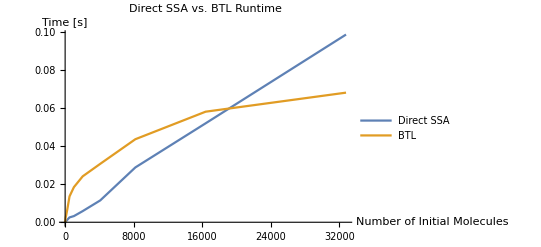

```mathematica
coorsBTL=Table[
Table[{resultsBTL[[i]][[l]][[2]],resultsBTL[[i]][[l]][[4]]["backend algorithm"]},{l,Length[resultsBTL[[i]]]}],
{i,Length[simulations]}];
simulationLabels={"Direct SSA","BTL"};
ListLinePlot[
coorsBTL,
PlotLegends->simulationLabels,
AxesLabel->{"Number of Initial Molecules","Time [s]"},
PlotLabel->"Direct SSA vs. BTL Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL.mx"},OperatingSystem->$OperatingSystem], resultsBTL];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL.mx"},OperatingSystem->$OperatingSystem], coorsBTL];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsBTL=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL.mx"},OperatingSystem->$OperatingSystem]]
coorsBTL=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL.mx"},OperatingSystem->$OperatingSystem]]
```

{{{SimulateDirectSSA,2,0.,<|frontend conversion→0.,interface conversion→0.0000133,backend preprocessing→0.000243,backend algorithm→0.0004158|>},{SimulateDirectSSA,4,0.,<|frontend conversion→0.,interface conversion→0.0000151,backend preprocessing→0.000108,backend algorithm→0.0000146|>},{SimulateDirectSSA,8,0.,<|frontend conversion→0.,interface conversion→8.9×10^-6,backend preprocessing→0.0000183,backend algorithm→0.000022|>},{SimulateDirectSSA,16,0.,<|frontend conversion→0.,interface conversion→8.2×10^-6,backend preprocessing→0.0000152,backend algorithm→0.0000457|>},{SimulateDirectSSA,32,0.015625,<|frontend conversion→0.,interface conversion→8.1×10^-6,backend preprocessing→0.0000175,backend algorithm→0.0000794|>},{SimulateDirectSSA,64,0.,<|frontend conversion→0.,interface conversion→8.3×10^-6,backend preprocessing→0.0000154,backend algorithm→0.0001772|>},{SimulateDirectSSA,128,0.,<|frontend conversion→0.,interface conversion→0.0000148,backend preprocessing→0.0000335,backend algorithm→0.0006223|>},{SimulateDirectSSA,256,0.,<|frontend conversion→0.,interface conversion→0.0000237,backend preprocessing→0.0000353,backend algorithm→0.0013147|>},{SimulateDirectSSA,512,0.,<|frontend conversion→0.,interface conversion→0.0000125,backend preprocessing→0.0000278,backend algorithm→0.0025492|>},{SimulateDirectSSA,1024,0.,<|frontend conversion→0.,interface conversion→0.0000127,backend preprocessing→0.0000296,backend algorithm→0.0032378|>},{SimulateDirectSSA,2048,0.,<|frontend conversion→0.,interface conversion→9.1×10^-6,backend preprocessing→0.0000557,backend algorithm→0.005855|>},{SimulateDirectSSA,4096,0.015625,<|frontend conversion→0.,interface conversion→0.0000106,backend preprocessing→0.0000224,backend algorithm→0.0114863|>},{SimulateDirectSSA,8192,0.03125,<|frontend conversion→0.,interface conversion→0.0000174,backend preprocessing→0.0000349,backend algorithm→0.0288267|>},{SimulateDirectSSA,16384,0.046875,<|frontend conversion→0.,interface conversion→5.9×10^-6,backend preprocessing→0.000024,backend algorithm→0.0520087|>},{SimulateDirectSSA,32768,0.09375,<|frontend conversion→0.,interface conversion→0.0000125,backend preprocessing→0.000048,backend algorithm→0.0986989|>}},{{SimulateBoundedTauLeaping,2,0.,<|frontend conversion→0.,interface conversion→0.000144,backend preprocessing→0.0000238,backend algorithm→0.0005483|>},{SimulateBoundedTauLeaping,4,0.,<|frontend conversion→0.,interface conversion→0.0000169,backend preprocessing→5.×10^-6,backend algorithm→0.0001691|>},{SimulateBoundedTauLeaping,8,0.,<|frontend conversion→0.,interface conversion→0.0000165,backend preprocessing→5.5×10^-6,backend algorithm→0.0003114|>},{SimulateBoundedTauLeaping,16,0.,<|frontend conversion→0.,interface conversion→0.0000111,backend preprocessing→3.×10^-6,backend algorithm→0.0004659|>},{SimulateBoundedTauLeaping,32,0.,<|frontend conversion→0.,interface conversion→0.0000199,backend preprocessing→5.3×10^-6,backend algorithm→0.0013937|>},{SimulateBoundedTauLeaping,64,0.,<|frontend conversion→0.,interface conversion→0.0000175,backend preprocessing→4.3×10^-6,backend algorithm→0.0024897|>},{SimulateBoundedTauLeaping,128,0.,<|frontend conversion→0.,interface conversion→0.0000132,backend preprocessing→3.8×10^-6,backend algorithm→0.003804|>},{SimulateBoundedTauLeaping,256,0.,<|frontend conversion→0.,interface conversion→0.0000177,backend preprocessing→4.×10^-6,backend algorithm→0.0068337|>},{SimulateBoundedTauLeaping,512,0.015625,<|frontend conversion→0.,interface conversion→0.0000131,backend preprocessing→3.1×10^-6,backend algorithm→0.0136011|>},{SimulateBoundedTauLeaping,1024,0.015625,<|frontend conversion→0.,interface conversion→0.0000141,backend preprocessing→3.×10^-6,backend algorithm→0.0184637|>},{SimulateBoundedTauLeaping,2048,0.03125,<|frontend conversion→0.,interface conversion→0.0000116,backend preprocessing→3.1×10^-6,backend algorithm→0.0241409|>},{SimulateBoundedTauLeaping,4096,0.03125,<|frontend conversion→0.,interface conversion→0.00001,backend preprocessing→2.4×10^-6,backend algorithm→0.0307193|>},{SimulateBoundedTauLeaping,8192,0.046875,<|frontend conversion→0.,interface conversion→0.0000237,backend preprocessing→3.6×10^-6,backend algorithm→0.043662|>},{SimulateBoundedTauLeaping,16384,0.0625,<|frontend conversion→0.,interface conversion→0.0000109,backend preprocessing→2.9×10^-6,backend algorithm→0.0581322|>},{SimulateBoundedTauLeaping,32768,0.0625,<|frontend conversion→0.,interface conversion→7.1×10^-6,backend preprocessing→4.2×10^-6,backend algorithm→0.0681508|>}}}

{{{2,0.0004158},{4,0.0000146},{8,0.000022},{16,0.0000457},{32,0.0000794},{64,0.0001772},{128,0.0006223},{256,0.0013147},{512,0.0025492},{1024,0.0032378},{2048,0.005855},{4096,0.0114863},{8192,0.0288267},{16384,0.0520087},{32768,0.0986989}},{{2,0.0005483},{4,0.0001691},{8,0.0003114},{16,0.0004659},{32,0.0013937},{64,0.0024897},{128,0.003804},{256,0.0068337},{512,0.0136011},{1024,0.0184637},{2048,0.0241409},{4096,0.0307193},{8192,0.043662},{16384,0.0581322},{32768,0.0681508}}}

## Direct SSA vs. BTL up to 1,000,000 molecules

```mathematica
simulations={SimulateDirectSSA,SimulateBoundedTauLeaping};
nRange=Table[10^i,{i,1,6}];
resultsBTL2=Table[TestSysBTL[ConstructSysMax,simulations[[i]],nRange],{i,Length[simulations]}];
```

{SimulateDirectSSA,10,0.,<|frontend conversion→0.,interface conversion→8.7×10^-6,backend preprocessing→0.0000287,backend algorithm→0.0000292|>}

{SimulateDirectSSA,100,0.,<|frontend conversion→0.,interface conversion→5.×10^-6,backend preprocessing→0.0000179,backend algorithm→0.0002243|>}

{SimulateDirectSSA,1000,0.,<|frontend conversion→0.,interface conversion→4.8×10^-6,backend preprocessing→0.0000153,backend algorithm→0.0033505|>}

{SimulateDirectSSA,10000,0.03125,<|frontend conversion→0.,interface conversion→8.5×10^-6,backend preprocessing→0.0000358,backend algorithm→0.0271152|>}

{SimulateDirectSSA,100000,0.265625,<|frontend conversion→0.,interface conversion→9.8×10^-6,backend preprocessing→0.0000299,backend algorithm→0.256969|>}

{SimulateDirectSSA,1000000,2.4375,<|frontend conversion→0.,interface conversion→0.0000114,backend preprocessing→0.000032,backend algorithm→2.47838|>}

{SimulateBoundedTauLeaping,10,0.,<|frontend conversion→0.,interface conversion→5.5×10^-6,backend preprocessing→2.6×10^-6,backend algorithm→0.00026|>}

{SimulateBoundedTauLeaping,100,0.015625,<|frontend conversion→0.,interface conversion→0.00001,backend preprocessing→4.2×10^-6,backend algorithm→0.0039898|>}

{SimulateBoundedTauLeaping,1000,0.015625,<|frontend conversion→0.,interface conversion→9.2×10^-6,backend preprocessing→4.×10^-6,backend algorithm→0.0171444|>}

{SimulateBoundedTauLeaping,10000,0.046875,<|frontend conversion→0.,interface conversion→7.9×10^-6,backend preprocessing→2.8×10^-6,backend algorithm→0.043678|>}

{SimulateBoundedTauLeaping,100000,0.109375,<|frontend conversion→0.,interface conversion→0.0000122,backend preprocessing→4.3×10^-6,backend algorithm→0.103076|>}

{SimulateBoundedTauLeaping,1000000,0.265625,<|frontend conversion→0.,interface conversion→5.2×10^-6,backend preprocessing→2.8×10^-6,backend algorithm→0.273262|>}

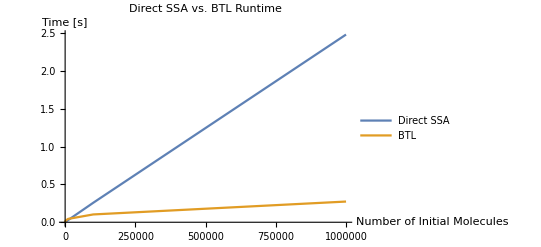

```mathematica
coorsBTL2=Table[
Table[{resultsBTL2[[i]][[l]][[2]],resultsBTL2[[i]][[l]][[4]]["backend algorithm"]},{l,Length[resultsBTL2[[i]]]}],
{i,Length[simulations]}];
simulationLabels={"Direct SSA","BTL"};
ListLinePlot[
coorsBTL2,
PlotLegends->simulationLabels,
AxesLabel->{"Number of Initial Molecules","Time [s]"},
PlotLabel->"Direct SSA vs. BTL Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL2.mx"},OperatingSystem->$OperatingSystem], resultsBTL2];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL2.mx"},OperatingSystem->$OperatingSystem], coorsBTL2];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsBTL2=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL2.mx"},OperatingSystem->$OperatingSystem]]
coorsBTL2=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL2.mx"},OperatingSystem->$OperatingSystem]]
```

{{{SimulateDirectSSA,10,0.,<|frontend conversion→0.,interface conversion→8.7×10^-6,backend preprocessing→0.0000287,backend algorithm→0.0000292|>},{SimulateDirectSSA,100,0.,<|frontend conversion→0.,interface conversion→5.×10^-6,backend preprocessing→0.0000179,backend algorithm→0.0002243|>},{SimulateDirectSSA,1000,0.,<|frontend conversion→0.,interface conversion→4.8×10^-6,backend preprocessing→0.0000153,backend algorithm→0.0033505|>},{SimulateDirectSSA,10000,0.03125,<|frontend conversion→0.,interface conversion→8.5×10^-6,backend preprocessing→0.0000358,backend algorithm→0.0271152|>},{SimulateDirectSSA,100000,0.265625,<|frontend conversion→0.,interface conversion→9.8×10^-6,backend preprocessing→0.0000299,backend algorithm→0.256969|>},{SimulateDirectSSA,1000000,2.4375,<|frontend conversion→0.,interface conversion→0.0000114,backend preprocessing→0.000032,backend algorithm→2.47838|>}},{{SimulateBoundedTauLeaping,10,0.,<|frontend conversion→0.,interface conversion→5.5×10^-6,backend preprocessing→2.6×10^-6,backend algorithm→0.00026|>},{SimulateBoundedTauLeaping,100,0.015625,<|frontend conversion→0.,interface conversion→0.00001,backend preprocessing→4.2×10^-6,backend algorithm→0.0039898|>},{SimulateBoundedTauLeaping,1000,0.015625,<|frontend conversion→0.,interface conversion→9.2×10^-6,backend preprocessing→4.×10^-6,backend algorithm→0.0171444|>},{SimulateBoundedTauLeaping,10000,0.046875,<|frontend conversion→0.,interface conversion→7.9×10^-6,backend preprocessing→2.8×10^-6,backend algorithm→0.043678|>},{SimulateBoundedTauLeaping,100000,0.109375,<|frontend conversion→0.,interface conversion→0.0000122,backend preprocessing→4.3×10^-6,backend algorithm→0.103076|>},{SimulateBoundedTauLeaping,1000000,0.265625,<|frontend conversion→0.,interface conversion→5.2×10^-6,backend preprocessing→2.8×10^-6,backend algorithm→0.273262|>}}}

{{{10,0.0000292},{100,0.0002243},{1000,0.0033505},{10000,0.0271152},{100000,0.256969},{1000000,2.47838}},{{10,0.00026},{100,0.0039898},{1000,0.0171444},{10000,0.043678},{100000,0.103076},{1000000,0.273262}}}